```mathematica
Remove["Global`*"]
(*Constants*)
```

```mathematica
c = 2.99792458*^8;
h = 6.62607004*^-34;
ℏ = h/(2π);
ϵo = 8.8541878128*^-12;
kb = 1.38064852*^-23;
e = 1.60217662*^-19;
a0 = 0.529177210903*^-10;
Be=.368h 100 c;
ωe=700 100 c 2 π;
```

```mathematica
(*Make the matrixes for the various transition Properties*)
m = (138 35)/(138 + 35) 1.67*^-27; (*reduced mass of the^138 Ba^+ +^35 Cl system in kg*)
vMax=3; (*maximum number of vibrational levels to include in the model*)
jMax=70; (*maximum number of rotational levels (per vibrational manifold) to include in the model*)
DCM=3.335×10^-30; (*conversion factor to convert dipole matrix elements calculated
```

```mathematica
TDM[vUp_,vDown_]=Piecewise[{{8.8,vUp==0&&vDown==0},
							{0.33,vUp==1&&vDown==0},
							{2.55×10^-2,vUp==2&&vDown==0},
							{2.35×10^-3,vUp==3&&vDown==0},
							{2.61×10^-4,vUp==4&&vDown==0},
							{3.36×10^-5,vUp==5&&vDown==0},
							{4.84×10^-6,vUp==6&&vDown==0},
						      {7.71×10^-7,vUp==7&&vDown==0},
							{1.32×10^-8,vUp==8&&vDown==0},
							{8.85,vUp==1&&vDown==1},
							{4.62×10^-1,vUp==2&&vDown==1},
							{4.43×10^-2,vUp==3&&vDown==1},
							{4.72×10^-3,vUp==4&&vDown==1},
							{5.87×10^-4,vUp==5&&vDown==1},
							{8.29×10^-5,vUp==6&&vDown==1},
							{1.31×10^-5,vUp==7&&vDown==1},
							{2.16×10^-6,vUp==8&&vDown==1},
							{8.9,vUp==2&&vDown==2},
							{5.63×10^-1,vUp==3&&vDown==2},
							{6.26×10^-2,vUp==4&&vDown==2},
							{7.49×10^-3,vUp==5&&vDown==2},
							{1.02×10^-3,vUp==6&&vDown==2},
							{1.57×10^-4,vUp==7&&vDown==2},
							{2.63×10^-2,vUp==8&&vDown==2},
							{8.95,vUp==3&&vDown==3},
							{6.47×10^-1,vUp==4&&vDown==3},
							{8.08×10^-2,vUp==5&&vDown==3},
							{1.06×10^-2,vUp==6&&vDown==3},
							{1.57×10^-3,vUp==7&&vDown==3},
							{2.59×10^-4,vUp==8&&vDown==3},



}]


TDM[1,0]
```

Piecewise[{{8.8, vUp==0&&vDown==0}, {0.33, vUp==1&&vDown==0}, {0, True}}]

0.33

```mathematica
master=Transpose[{rotDown,rotUp,vDown,vUp,dm,enDiff,Acoe}]; (*master array of all transitions and their properties*)
```

```mathematica
DMmasterUP=Gather[#,#1[[1]]==#2[[1]] &]&/@Gather[Select[master,#[[1]]<jMax  &&  #[[2]]<jMax && #[[3]]<vMax && #[[4]]<vMax &],#1[[3]]==#2[[3]] &]; (*these arrays contain all transition that start from a particular transition and go upward, useful for stimulated absorption*)
EnmasterUP= Gather[#,#1[[1]]==#2[[1]]&]&/@Gather[Select[master,#[[1]]<jMax  && #[[2]]<jMax && #[[3]]<vMax && #[[4]]<vMax &],#1[[3]]==#2[[3]] &];
DMslimUP=DCM Table[Table[If[i==vMax && j==jMax,{0},DMmasterUP[[i]][[j]][[;;,5]]],{j,1,jMax}],{i,1,vMax}];
enSlimUP=2 π 100 c Quiet[ Table[Table[If[i==vMax && j==jMax,{1*^-10},EnmasterUP[[i]][[j]][[;;,6]]],{j,1,jMax}],{i,1,vMax}]];
HonlUP=Table[Table[Table[If[i==vMax && j==jMax+1,{0},If [EnmasterUP[[i]][[j]][[;;,2]][[k]]>EnmasterUP[[i]][[j]][[;;,1]][[k]],(EnmasterUP[[i]][[j]][[;;,1]][[k]]+1)/(2EnmasterUP[[i]][[j]][[;;,2]][[k]]+1),EnmasterUP[[i]][[j]][[;;,1]][[k]]/(2EnmasterUP[[i]][[j]][[;;,2]][[k]]+1)]],{k,1,EnmasterUP[[i]][[j]][[;;,1]]//Length,1}],{j,1,jMax}],{i,1,vMax}];
HonlUP[[vMax]][[jMax]]={0};
AmasterUP=Abs[2/3 1/(ϵo h c^3)(enSlimUP)^3(DMslimUP)^2 HonlUP];
BcoeUP=Table[Table[Table[(2EnmasterUP[[i]][[j]][[;;,2]][[k]]+1)/(2EnmasterUP[[i]][[j]][[;;,1]][[k]]+1),{k,1,EnmasterUP[[i]][[j]][[;;,1]]//Length,1}],{j,1,jMax}],{i,1,vMax}];
BcoeUP[[vMax]][[jMax]]={0};

AcoeUP= Table[Table[DMmasterUP[[i]][[j]][[;;,7]],{j,1,jMax}],{i,1,vMax}];
Babsorp=Abs[1/8 c^2/(π h)(enSlimUP/(2 π)  )^-3*AcoeUP*BcoeUP];
Babsorpe=Abs[1/8 c^2/(π h)(enSlimUP/(2 π))^-3*AcoeUP];
```

Part::partw: Part 99 of {{{0,1,19,19,10.1885,0.16,4.83619×10^-8}},{{1,2,19,19,10.1885,0.33,4.64275×10^-7}},{{2,3,19,19,10.1886,0.49,1.67884×10^-6}},{{3,4,19,19,10.1886,0.66,4.12684×10^-6}},{{4,5,19,19,10.1887,0.82,8.24338×10^-6}},«41»,{{46,47,19,19,10.2016,7.72,0.00744349}},{{47,48,19,19,10.2021,7.89,0.00793012}},{{48,49,19,19,10.2027,8.05,0.00843748}},{{49,50,19,19,10.2033,8.22,0.00896601}},«48»} does not exist.

Part::partd: Part specification «1» is longer than depth of object.

Part::partw: Part 99 of {{{0,1,19,19,10.1885,0.16,4.83619×10^-8}},{{1,2,19,19,10.1885,0.33,4.64275×10^-7}},{{2,3,19,19,10.1886,0.49,1.67884×10^-6}},{{3,4,19,19,10.1886,0.66,4.12684×10^-6}},{{4,5,19,19,10.1887,0.82,8.24338×10^-6}},«41»,{{46,47,19,19,10.2016,7.72,0.00744349}},{{47,48,19,19,10.2021,7.89,0.00793012}},{{48,49,19,19,10.2027,8.05,0.00843748}},{{49,50,19,19,10.2033,8.22,0.00896601}},«48»} does not exist.

Part::partd: Part specification «1» is longer than depth of object.

Part::partw: Part 99 of {{{0,1,19,19,10.1885,0.16,4.83619×10^-8}},{{1,2,19,19,10.1885,0.33,4.64275×10^-7}},{{2,3,19,19,10.1886,0.49,1.67884×10^-6}},{{3,4,19,19,10.1886,0.66,4.12684×10^-6}},{{4,5,19,19,10.1887,0.82,8.24338×10^-6}},«41»,{{46,47,19,19,10.2016,7.72,0.00744349}},{{47,48,19,19,10.2021,7.89,0.00793012}},{{48,49,19,19,10.2027,8.05,0.00843748}},{{49,50,19,19,10.2033,8.22,0.00896601}},«48»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification «1» is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 99 of {{{0,1,19,19,10.1885,0.16,4.83619×10^-8}},{{1,2,19,19,10.1885,0.33,4.64275×10^-7}},{{2,3,19,19,10.1886,0.49,1.67884×10^-6}},{{3,4,19,19,10.1886,0.66,4.12684×10^-6}},{{4,5,19,19,10.1887,0.82,8.24338×10^-6}},«41»,{{46,47,19,19,10.2016,7.72,0.00744349}},{{47,48,19,19,10.2021,7.89,0.00793012}},{{48,49,19,19,10.2027,8.05,0.00843748}},{{49,50,19,19,10.2033,8.22,0.00896601}},«48»} does not exist.

Part::partd: Part specification «1» is longer than depth of object.

Part::partw: Part 99 of {{{0,1,19,19,10.1885,0.16,4.83619×10^-8}},{{1,2,19,19,10.1885,0.33,4.64275×10^-7}},{{2,3,19,19,10.1886,0.49,1.67884×10^-6}},{{3,4,19,19,10.1886,0.66,4.12684×10^-6}},{{4,5,19,19,10.1887,0.82,8.24338×10^-6}},«41»,{{46,47,19,19,10.2016,7.72,0.00744349}},{{47,48,19,19,10.2021,7.89,0.00793012}},{{48,49,19,19,10.2027,8.05,0.00843748}},{{49,50,19,19,10.2033,8.22,0.00896601}},«48»} does not exist.

Part::partd: Part specification «1» is longer than depth of object.

Part::partw: Part 99 of {{{0,1,19,19,10.1885,0.16,4.83619×10^-8}},{{1,2,19,19,10.1885,0.33,4.64275×10^-7}},{{2,3,19,19,10.1886,0.49,1.67884×10^-6}},{{3,4,19,19,10.1886,0.66,4.12684×10^-6}},{{4,5,19,19,10.1887,0.82,8.24338×10^-6}},«41»,{{46,47,19,19,10.2016,7.72,0.00744349}},{{47,48,19,19,10.2021,7.89,0.00793012}},{{48,49,19,19,10.2027,8.05,0.00843748}},{{49,50,19,19,10.2033,8.22,0.00896601}},«48»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification «1» is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 99 of {{{0,1,19,19,10.1885,0.16,4.83619×10^-8}},{{1,2,19,19,10.1885,0.33,4.64275×10^-7}},{{2,3,19,19,10.1886,0.49,1.67884×10^-6}},{{3,4,19,19,10.1886,0.66,4.12684×10^-6}},{{4,5,19,19,10.1887,0.82,8.24338×10^-6}},«41»,{{46,47,19,19,10.2016,7.72,0.00744349}},{{47,48,19,19,10.2021,7.89,0.00793012}},{{48,49,19,19,10.2027,8.05,0.00843748}},{{49,50,19,19,10.2033,8.22,0.00896601}},«48»} does not exist.

Part::partd: Part specification «1» is longer than depth of object.

```mathematica
(*these arrays contain all transition that start from a particular transition and go downward, useful for stimulated emission and spontaneous emission*)
DMmasterDOWN=Gather[#,#1[[2]]==#2[[2]] &]&/@Gather[Select[master,#[[1]]<jMax   && #[[3]]≤ vMax && #[[4]]≤ vMax &],#1[[4]]==#2[[4]] &];
EnmasterDOWN= Gather[#,#1[[2]]==#2[[2]]&]&/@Gather[Select[master,#[[1]]<jMax    && #[[3]]≤ vMax && #[[4]]≤ vMax &],#1[[4]]==#2[[4]] &];
DMmasterDOWN[[1]]=Prepend[DMmasterDOWN[[1]],{{0,0,0,0,0,0,0}}];
EnmasterDOWN[[1]]=Prepend[EnmasterDOWN[[1]],{{0,0,0,0,0,.1,0}}];
DMslimDOWN=DCM Table[Table[DMmasterDOWN[[i]][[j]][[;;,5]],{j,1,jMax}],{i,1,vMax}];
enSlimDOWN=Table[Table[ 2 π 100  c EnmasterDOWN[[i]][[j]][[;;,6]],{j,1,jMax}],{i,1,vMax}];


JDOWN=Table[Table[DMmasterDOWN[[i]][[j]][[;;,1]],{j,1,jMax}],{i,1,vMax}];
Jup=Table[Table[EnmasterDOWN[[i]][[j]][[;;,2]],{j,1,jMax}],{i,1,vMax}];
HonlDOWN=Table[Table[Table[If [EnmasterDOWN[[i]][[j]][[;;,2]][[k]]>EnmasterDOWN[[i]][[j]][[;;,1]][[k]],(EnmasterDOWN[[i]][[j]][[;;,1]][[k]]+1)/(2EnmasterDOWN[[i]][[j]][[;;,2]][[k]]+1),EnmasterDOWN[[i]][[j]][[;;,1]][[k]]/(2EnmasterDOWN[[i]][[j]][[;;,2]][[k]]+1)],{k,1,EnmasterDOWN[[i]][[j]][[;;,1]]//Length,1}],{j,1,jMax}],{i,1,vMax}];

BcoeDOWN=Table[Table[Table[(2EnmasterDOWN[[i]][[j]][[;;,2]][[k]]+1)/(2EnmasterDOWN[[i]][[j]][[;;,1]][[k]]+1),{k,1,EnmasterDOWN[[i]][[j]][[;;,1]]//Length,1}],{j,1,jMax}],{i,1,vMax}];

AmasterDOWN=Abs[2/3 1/(ϵo h c^3)(enSlimDOWN)^3(DMslimDOWN)^2*HonlDOWN];
AcoeDOWN= Table[Table[DMmasterDOWN[[i]][[j]][[;;,7]],{j,1,jMax}],{i,1,vMax}];
```

```mathematica
(*absorption coefficient*)
```

```mathematica
Bemission=Abs[1/8 c^2/(π h)(enSlimDOWN/(2 π) )^-3*AcoeDOWN];
Bemmsiona=Abs[1/8 c^2/(π h)(enSlimDOWN/(2 π))^-3*AcoeDOWN*BcoeDOWN];
```

```mathematica
T=300; (*internal temp of BaCl^+sample in Kelvin*)
(*set of master equations including just BBR*)
masterEqns=Table[Table[Subscript[n, i,j]'[t]== -Total[AmasterDOWN[[i+1]][[j+1]]]Subscript[n, i,j][t](*spon emission out*)

+If[i==vMax-1 && j==jMax-1,0,Sum[AmasterUP[[i+1,j+1]][[k]]Subscript[n, DMmasterUP[[i+1,j+1]][[k]][[4]],DMmasterUP[[i+1,j+1]][[k]][[2]]][t],{k,1,AmasterUP[[i+1]][[j+1]]//Length}]](*spon emission in*)

+If[i==vMax-1 && j==jMax-1,0,Sum[(8π h((enSlimUP[[i+1,j+1]][[k]])/(2 π))^3)/(c^2(Exp[(ℏ enSlimUP[[i+1,j+1]][[k]])/(kb T)]-1))Babsorpe[[i+1,j+1]][[k]]Subscript[n, DMmasterUP[[i+1,j+1]][[k]][[4]],DMmasterUP[[i+1,j+1]][[k]][[2]]][t],{k,1,DMmasterUP[[i+1]][[j+1]]//Length}]]+If[i==vMax-1 && j==jMax-1,0,Sum[(8π h((enSlimUP[[i+1,j+1]][[k]])/(2 π))^3)/(c^2(Exp[(ℏ enSlimUP[[i+1,j+1]][[k]])/(kb T)]-1))(-Babsorp[[i+1,j+1]][[k]]Subscript[n, i,j][t]),{k,1,Babsorp[[i+1]][[j+1]]//Length}]]

(*BBR stimulated absorption*)
+Sum[(8π h((enSlimDOWN[[i+1,j+1]][[k]])/(2 π))^3)/(c^2(Exp[(ℏ enSlimDOWN[[i+1,j+1]][[k]])/(kb T)]-1))(-Bemission[[i+1,j+1]][[k]]Subscript[n, i,j][t])
(*BBR stimulated emission*)

,{k,1,Bemission[[i+1]][[j+1]]//Length}]+Sum[(8π h((enSlimDOWN[[i+1,j+1]][[k]])/(2 π))^3)/(c^2(Exp[(ℏ enSlimDOWN[[i+1,j+1]][[k]])/(kb T)]-1))(Bemmsiona[[i+1,j+1]][[k]]Subscript[n, DMmasterDOWN[[i+1,j+1]][[k]][[3]],DMmasterDOWN[[i+1,j+1]][[k]][[1]]][t])
(*BBR stimulated emission*)

,{k,1,DMmasterDOWN[[i+1]][[j+1]]//Length}]
,{i,0,vMax-1}],{j,0,jMax-1}];
```

```mathematica
(*here I set the initial conditions to be perverse, all the pop starts in the highest state*)

initialCon={};
Do[Do[AppendTo[initialCon
,Subscript[n, i,j][0]==0],{i,0,vMax-1}],{j,0,jMax-1}];
initialCon[[61]]=(Subscript[n, 0,3][0]== 1);
eqnSolve={};

(*array containing all depedent variables*)
Do[Do[AppendTo[eqnSolve
,Subscript[n, i,j][t]],{i,0,vMax-1}],{j,0,jMax-1}];
totalEqns={};
Do[Do[AppendTo[totalEqns
,masterEqns[[i]][[j]]],{i,1,jMax}],{j,1,vMax}];
```

```mathematica
Flatten[masterEqns]//Length
eqnSolve//Length
initialCon//Length
```

1980

1980

1980

```mathematica
sln=NDSolve[Join[totalEqns,initialCon],Reverse[eqnSolve],{t,0,120000},Method->{"EquationSimplification"->"Residual"}];
```

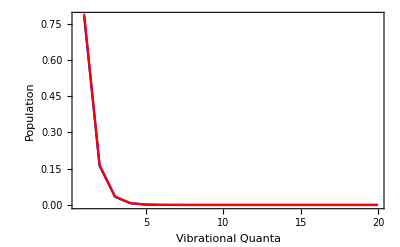

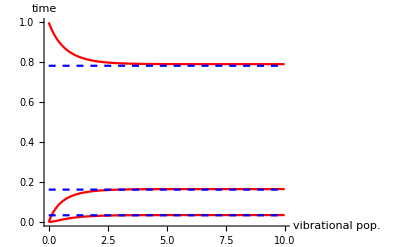

```mathematica
(*to make sure i didn't mess up, let's compare to a Maxwell Boltzmann distribution to if they have agreement*)

Be=.09 h 100 c;
ωe=328 100 c 2 π;
vibMaxBoltz[v_,T_]:=(Exp[-ℏ ωe/(2kb T)](1-Exp[-ℏ ωe/(kb T)])^-1)^-1 Exp[-ℏ (ωe(v+1/2))/(kb T)]
MaxBoltz[v_,J_,T_]:=vibMaxBoltz[v,T]((2J+1)Exp[-(Be J(J+1))/(kb T)])/Sum[(2k+1)Exp[-(Be k(k+1))/(kb T)],{k,0,300}]

(*for comparison of Max-Boltz vibrational populations with model, sum over rotational levels*)
vibLevel=0;
vib1[t_]=Total[Table[Sum[Subscript[n, i,j][t]/.sln,{j,0,jMax-1}],{i,vibLevel,vibLevel}]];
vibLevel=1;
vib2[t_]=Total[Table[Sum[Subscript[n, i,j][t]/.sln,{j,0,jMax-1}],{i,vibLevel,vibLevel}]];
vibLevel=2;
vib3[t_]=Total[Table[Sum[Subscript[n, i,j][t]/.sln,{j,0,jMax-1}],{i,vibLevel,vibLevel}]];
MBVib=Table[Sum[MaxBoltz[i,k,T],{k,0,jMax-1}],{i,0,vMax-1}];

tProbe=10;

(*this plots the expected vibrational populations for both the model and Max-Boltz predicitons at a time tProbe*)
Show[ListLinePlot[MBVib,PlotRange->All,PlotStyle->Blue,Frame->True,FrameLabel->{"Vibrational Quanta","Population"}],ListLinePlot[Flatten[Table[Sum[Subscript[n, i,j][t]/.sln,{j,0,jMax-1}]/.t->tProbe,{i,0,vMax-1}]],PlotStyle->Red,PlotRange->All]]

(*this plots the expected vibrational populations for both the model and Max-Boltz predicitons at a time tProbe*)
Show[Plot[{vib1[t],vib2[t],vib3[t]},{t,0,10},PlotRange->All,PlotStyle->Red,AxesLabel->{"vibrational pop.","time"}],Plot[{Sum[MaxBoltz[0,k,T],{k,0,100}],Sum[MaxBoltz[2,k,T],{k,0,100}],Sum[MaxBoltz[1,k,T],{k,0,100}]},{t,0,10},PlotStyle->Table[{Blue,Dashed},{i,1,3}]]]

(*looks pretty good*)
```

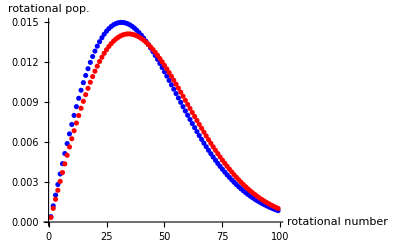

```mathematica
(*Now let's look at rotational level populations*)
tProbe=2000;
rotationalPop=Flatten[Table[Subscript[n, 0,J][t]/.sln/.t->tProbe,{J,0,jMax-1}]];
MBrotPop=Table[MaxBoltz[0,J,T],{J,0,jMax-1}];
ListPlot[{rotationalPop,MBrotPop},AxesLabel->{"rotational number","rotational pop."},PlotStyle->{Blue,{Red,Dashed}},PlotRange->All]

(*okay, it looks in model the molecules aren't equillibrated rotationally, even at 10000 sec. Blackbody spectrum isn't peaked very strongly in the microwave regime so this isn't surprising. But the lack of equillibriation is also partly because I started with crazy initial conditions. If I make it more reasonable, the boltzman distribution should be fine, or I could just wait longer for the populations to redistribute. But I can't propogate my rate equation model past 10000 sec without crashing my computer so I'm going to leave it for now*)
```